```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yuichirotada/Documents/Univ/SLattice/peak_theory

## Peak Theory

```mathematica
npeak=16;
NL=256;
L=10^-12;(*Mpc*)
kpeak=2π npeak/NL;
```

### Monochromatic

```mathematica
f[x_]=1/2 x(x^2-3)(Erf[1/2 Sqrt[5/2]x]+Erf[Sqrt[5/2]x])+Sqrt[2/(5π)]((8/5+31/4 x^2)Exp[-5/8 x^2]+(-8/5+1/2 x^2)Exp[-5/2 x^2]);
nnu2PT[nu2_,ks_]=ks^3/(6π)^(3/2) f[nu2] 1/Sqrt[2π] Exp[-nu2^2/2];
```

```mathematica
Cm[nu2_,As_]=2/3(1-(1+xm Sinc'[xm]Sqrt[As]nu2)^2)/.{xm->2.74};
```

```mathematica
dlnMdmu2[nu2_,As_]=2Sqrt[As]Sinc[xm]+γ/(Cm[nu2,As]-Cth)D[Cm[nu2,As], nu2]/.{Cth->0.533,γ->0.36,xm->2.74}//Simplify;
```

```mathematica
nPBHpk[nu2_,ks_,As_]=nnu2PT[nu2,ks]/Abs[dlnMdmu2[nu2,As]];
```

```mathematica
Mpk[nu2_,As_]=xm^2 Exp[2Sqrt[As]Sinc[xm]nu2](Cm[nu2,As]-Cth)^γ/.{Cth->0.533,γ->0.36,xm->2.74};
Mks[ks_]=(NL/L ks/(1.56 10^13))^-2;
```

```mathematica
fPBHpk[nu2_,ks_,As_]=Mks[ks] Mpk[nu2,As] nPBHpk[nu2,ks,As]/(3.95 10^-20);
```

```mathematica
Mkpeak=Mks[kpeak]
```

0.0240796

```mathematica
Azeta=3.625 10^-3;
nu2th=nu2/.FindRoot[Cm[nu2,Azeta]==0.533,{nu2,8}];
fPBHpkList=Table[{Mkpeak Mpk[nu2th+10^dlnnu2,Azeta],fPBHpk[nu2th+10^dlnnu2,kpeak,Azeta]},{dlnnu2,-5,1/2,10^-2}];
```

```mathematica
Mmin=First[fPBHpkList][[1]]
Mmax=Last[fPBHpkList][[1]]
```

0.00102593

0.0943306

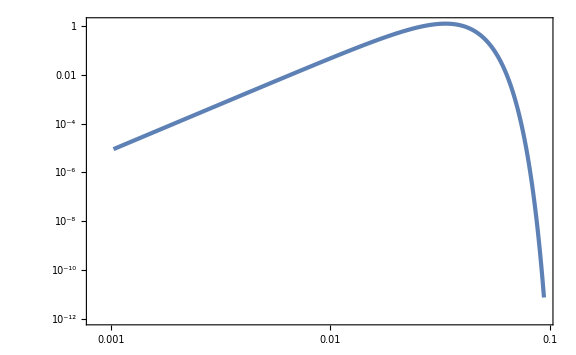

```mathematica
ListLogLogPlot[fPBHpkList]
```

```mathematica
fPBHpkint[M_]=Interpolation[fPBHpkList][M];
NIntegrate[fPBHpkint[M]/M,{M,Mmin,Mmax}]
```

1.00416

```mathematica
Export["data/fPBH_pk_mono.csv",fPBHpkList];
```

## Importance Sampling

### Monochromatic